```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[LogPlot,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Thick},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[LogLogPlot,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Thick},TicksStyle->Directive[Black,10],Frame->True];
```

# transmission of glass cell didn’t readjust focus; optimized focus of imaging lens at AOI = 0, so other data is a lower bound and not necessarily proportional, but it should be the same order of magnitude (redid roughly while refocusing to confirm)

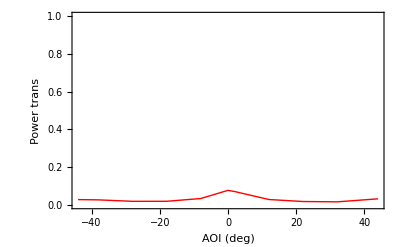

```mathematica
AOI={188,180,170,160,150,144,190,200,210,220,232}-188;
t={119,52.2,29.8,29.5,41.3,43.6,109,44.3,27.9,25.2,49.8} 10^-3/1.54;

dataT=Thread[{AOI,t}];
dataT=SortBy[dataT,First];
ListPlot[dataT,Joined->True,AxesLabel->{"AOI (deg)","Power trans"},PlotRange->{All,{0,1}}]
```

# reflection of glass cell. Re optimized focus of imaging lens at each AOI

{{-46,0.63961},{-38,0.655844},{-28,0.688312},{-20,0.655844},{22,0.694805},{32,0.681818},{46,0.631818}}

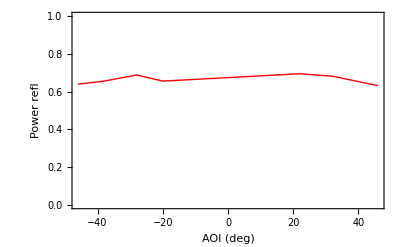

```mathematica
AOI={234,220,210,142,150,160,168}-188;
r={.973,1.05,1.07,.985,1.01,1.06,1.01}/1.54;

dataR=Thread[{AOI,r}];
dataR=SortBy[dataR,First]
ListPlot[dataR,Joined->True,AxesLabel->{"AOI (deg)","Power refl"},PlotRange->{All,{0,1}}]
```

# reflection of glass cylinder. Re optimized focus of imaging lens at each AOI

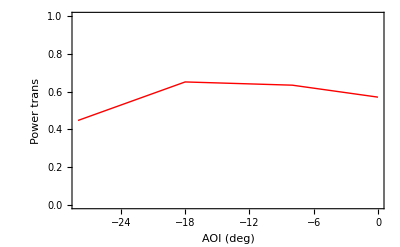

```mathematica
AOI={188,180,170,160}-188;
t2={.999,1.11,1.14,.783}/1.75;

dataT2=Thread[{AOI,t2}];
dataT2=SortBy[dataT2,First];
ListPlot[dataT2,Joined->True,AxesLabel->{"AOI (deg)","Power trans"},PlotRange->{All,{0,1}}]
```

# transmission of glass cell 2 (larger angles)

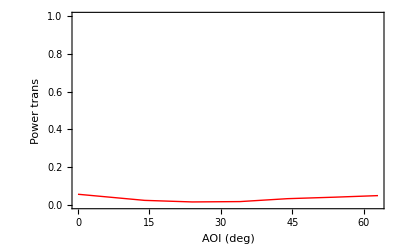

```mathematica
AOI={146,160,170,180,190,200,209}-146;
t={90.5,38.7,25.4,28.4,53.1,65.9,79} 10^-3/1.6;

dataT3=Thread[{AOI,t}];
dataT3=SortBy[dataT3,First];
ListPlot[dataT3,Joined->True,AxesLabel->{"AOI (deg)","Power trans"},PlotRange->{All,{0,1}}]
```